```mathematica
σ11=4.42*10^-8;
eps11=(8.16*10^-15);

σ12=4.26*10^-8;
eps12=(7.95*10^-14);
(*potential11[r_]=If[r<2.5*σ11,eps11((σ11/r)^12-(σ11/r)^6),0];
potential12[r_]=If[r<2.5*σ12,eps12((σ12/r)^12-(σ12/r)^6),0];*)
potential11[r_]=eps11((σ11/r)^12-(σ11/r)^6);
potential12[r_]=eps12((σ12/r)^12-(σ12/r)^6);
f11[r_]=D[potential11[r],r];
f12[r_]=D[potential12[r],r];

force11[r_]=If[r<2.5*σ11,f11[r],0];
force12[r_]=If[r<2.5*σ12,f12[r],0];
```

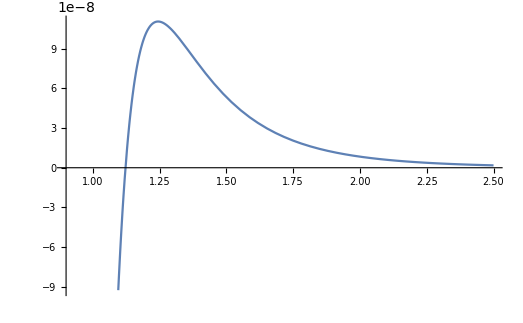

```mathematica
Plot[{force11[σ11 r]},{r,0.9,2.5}]
```

```mathematica
2.5*σ11
```

1.105×10^-7

```mathematica
dims[[1]]-(xCell2/2)
```

1.27335×10^-6

```mathematica
dims={13.06*10^-7,13.06*10^-7,6.53*10^-7};
(*dims={13.176*10^-7,13.176*10^-7,6.588*10^-7};*)

domainParts=100;
wallPartsX = 40;
wallPartsZ = 20;

wallPartsX2 = 20;
wallPartsZ2 = 10;

wallTotal = wallPartsX*wallPartsZ; 
spring=1;

xCell = dims[[1]]/wallPartsX;
zCell = dims[[3]]/wallPartsZ;

xCell2 = dims[[1]]/wallPartsX2;
zCell2 = dims[[3]]/wallPartsZ2;
dx=dims[[1]]/64;
xCell
zCell

wallPosBottom = Flatten[Table[{xCell/2+xCell*ii,0.25*dims[[2]],zCell/2+zCell*jj,spring},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosTop = Flatten[Table[{xCell/2+xCell*ii,0.75dims[[2]],zCell/2+zCell*jj,spring},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosBottom2 = Flatten[Table[{xCell2/2+xCell2*ii,0.25*dims[[2]]-2dx,zCell2/2+zCell2*jj,spring},{ii,0,wallPartsX2-1},{jj,0,wallPartsZ2-1}],1];
wallPosTop2 = Flatten[Table[{xCell2/2+xCell2*ii,0.75dims[[2]]+2dx,zCell2/2+zCell2*jj,spring},{ii,0,wallPartsX2-1},{jj,0,wallPartsZ2-1}],1];
b13=0;
b2=0.09;
domainPos = Table[{b13*dims[[1]]+RandomReal[]*(1-2b13)*dims[[1]],(0.25+b2)*dims[[2]]+RandomReal[]*(0.5-2b2)*dims[[2]],b13*dims[[3]]+RandomReal[]*(1-2b13)*dims[[3]],0},{ii,1,domainParts}];
domainPosGL=Table[{domainPos[[ii,1]]-dims[[1]],domainPos[[ii,2]],domainPos[[ii,3]],domainPos[[ii,4]]},{ii,1,Length[domainPos]}];
domainPosGR=Table[{domainPos[[ii,1]]+dims[[1]],domainPos[[ii,2]],domainPos[[ii,3]],domainPos[[ii,4]]},{ii,1,Length[domainPos]}];
domainPosGF=Table[{domainPos[[ii,1]],domainPos[[ii,2]],domainPos[[ii,3]]+dims[[3]],domainPos[[ii,4]]},{ii,1,Length[domainPos]}];
domainPosGB=Table[{domainPos[[ii,1]],domainPos[[ii,2]],domainPos[[ii,3]]-dims[[3]],domainPos[[ii,4]]},{ii,1,Length[domainPos]}];
domainPosGFL=Table[{domainPos[[ii,1]]-dims[[1]],domainPos[[ii,2]],domainPos[[ii,3]]+dims[[3]],domainPos[[ii,4]]},{ii,1,Length[domainPos]}];
domainPosGFR=Table[{domainPos[[ii,1]]+dims[[1]],domainPos[[ii,2]],domainPos[[ii,3]]+dims[[3]],domainPos[[ii,4]]},{ii,1,Length[domainPos]}];
domainPosGBL=Table[{domainPos[[ii,1]]-dims[[1]],domainPos[[ii,2]],domainPos[[ii,3]]-dims[[3]],domainPos[[ii,4]]},{ii,1,Length[domainPos]}];
domainPosGBR=Table[{domainPos[[ii,1]]+dims[[1]],domainPos[[ii,2]],domainPos[[ii,3]]-dims[[3]],domainPos[[ii,4]]},{ii,1,Length[domainPos]}];

wallPosBottomGL = Flatten[Table[{xCell/2+xCell*ii-dims[[1]],0.25*dims[[2]],xCell/2+zCell*jj,spring},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosBottomGR = Flatten[Table[{xCell/2+xCell*ii+dims[[1]],0.25*dims[[2]],xCell/2+zCell*jj,spring},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];

wallPosBottomGF = Flatten[Table[{xCell/2+xCell*ii,0.25*dims[[2]],xCell/2+zCell*jj+dims[[3]],spring},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosBottomGB = Flatten[Table[{xCell/2+xCell*ii,0.25*dims[[2]],xCell/2+zCell*jj-dims[[3]],spring},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosBottomGBL = Flatten[Table[{xCell/2+xCell*ii-dims[[1]],0.25*dims[[2]],xCell/2+zCell*jj-dims[[3]],spring},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosBottomGBR = Flatten[Table[{xCell/2+xCell*ii+dims[[1]],0.25*dims[[2]],xCell/2+zCell*jj-dims[[3]],spring},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosBottomGFL = Flatten[Table[{xCell/2+xCell*ii-dims[[1]],0.25*dims[[2]],xCell/2+zCell*jj+dims[[3]],spring},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosBottomGFR = Flatten[Table[{xCell/2+xCell*ii+dims[[1]],0.25*dims[[2]],xCell/2+zCell*jj+dims[[3]],spring},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];


wallPosTopGL = Flatten[Table[{xCell/2+xCell*ii-dims[[1]],0.75*dims[[2]],xCell/2+zCell*jj,spring},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosTopGR = Flatten[Table[{xCell/2+xCell*ii+dims[[1]],0.75*dims[[2]],xCell/2+zCell*jj,spring},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];

wallPosTopGF = Flatten[Table[{xCell/2+xCell*ii,0.75*dims[[2]],xCell/2+zCell*jj+dims[[3]],spring},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosTopGB = Flatten[Table[{xCell/2+xCell*ii,0.75*dims[[2]],xCell/2+zCell*jj-dims[[3]],spring},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosTopGBL = Flatten[Table[{xCell/2+xCell*ii-dims[[1]],0.75*dims[[2]],xCell/2+zCell*jj-dims[[3]],spring},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosTopGBR = Flatten[Table[{xCell/2+xCell*ii+dims[[1]],0.75*dims[[2]],xCell/2+zCell*jj-dims[[3]],spring},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosTopGFL = Flatten[Table[{xCell/2+xCell*ii-dims[[1]],0.75*dims[[2]],xCell/2+zCell*jj+dims[[3]],spring},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
wallPosTopGFR = Flatten[Table[{xCell/2+xCell*ii+dims[[1]],0.75*dims[[2]],xCell/2+zCell*jj+dims[[3]],spring},{ii,0,wallPartsX-1},{jj,0,wallPartsZ-1}],1];
```

3.265×10^-8

3.265×10^-8

```mathematica
For[mm=1,mm≤10,mm++,
maxForce=0;
For[i=1,i≤domainParts,i++,
force=0;
For[j=1,j≤domainParts,j++,
If[i≠j,
nvec=(domainPos[[i]]-domainPos[[j]])[[1;;3]];
dist=Norm[nvec];
(*force=force+force11[dist] nvec/dist;*)
force=force+force11[dist] nvec/dist;
];
nvec=(domainPos[[i]]-domainPosGL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
nvec=(domainPos[[i]]-domainPosGR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
nvec=(domainPos[[i]]-domainPosGF[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
nvec=(domainPos[[i]]-domainPosGB[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
nvec=(domainPos[[i]]-domainPosGFL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
nvec=(domainPos[[i]]-domainPosGFR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
nvec=(domainPos[[i]]-domainPosGBL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
nvec=(domainPos[[i]]-domainPosGBR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
];
(*For[j=1,j≤wallTotal,j++,
nvec=(domainPos[[i]]-wallPosBottom[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGF[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGB[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGFL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGFR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGBL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGBR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;


nvec=(domainPos[[i]]-wallPosTop[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGF[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGB[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGFL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGFR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGBL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGBR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
];*)
If[Norm[force] > maxForce,
maxForce = Norm[force];
maxi = i;
];
];
(*Print[maxForce];*)
maxOld = maxForce;
domainOld=domainPos[[maxi]];
domainPos[[maxi]] = {b13*dims[[1]]+RandomReal[]*(1-2b13)*dims[[1]],(0.25+b2)*dims[[2]]+RandomReal[]*(0.5-2b2)*dims[[2]],b13*dims[[3]]+RandomReal[]*(1-2b13)*dims[[3]],0};
domainPosGL[[maxi]] =domainPos[[maxi]] -{dims[[1]],0,0,0};
domainPosGR[[maxi]] =domainPos[[maxi]] +{dims[[1]],0,0,0};
domainPosGB[[maxi]] =domainPos[[maxi]] -{0,0,dims[[3]],0};
domainPosGF[[maxi]] =domainPos[[maxi]] +{0,0,dims[[3]],0};

domainPosGFL[[maxi]] =domainPos[[maxi]] +{-dims[[1]],0,dims[[3]],0};
domainPosGFR[[maxi]] =domainPos[[maxi]] +{dims[[1]],0,dims[[3]],0};
domainPosGBL[[maxi]] =domainPos[[maxi]] +{-dims[[1]],0,-dims[[3]],0};
domainPosGBR[[maxi]] =domainPos[[maxi]] +{dims[[1]],0,-dims[[3]],0};
maxForce=0;
For[i=1,i≤domainParts,i++,
force=0;
For[j=1,j≤domainParts,j++,
If[i≠j,
nvec={domainPos[[i,1]]-domainPos[[j,1]],domainPos[[i,2]]-domainPos[[j,2]],domainPos[[i,3]]-domainPos[[j,3]]};
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
];
nvec=(domainPos[[i]]-domainPosGL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
nvec=(domainPos[[i]]-domainPosGR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
nvec=(domainPos[[i]]-domainPosGF[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
nvec=(domainPos[[i]]-domainPosGB[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
nvec=(domainPos[[i]]-domainPosGFL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
nvec=(domainPos[[i]]-domainPosGFR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
nvec=(domainPos[[i]]-domainPosGBL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
nvec=(domainPos[[i]]-domainPosGBR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
];
(*For[j=1,j≤wallTotal,j++,

nvec=(domainPos[[i]]-wallPosBottom[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGF[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGB[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGFL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGFR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGBL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGBR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;


nvec=(domainPos[[i]]-wallPosTop[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGF[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGB[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGFL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGFR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGBL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGBR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
];*)
If[Norm[force] > maxForce,
maxForce = Norm[force];

];
];
maxForceNew = maxForce;

If[maxForceNew > maxOld,
domainPos[[maxi]]=domainOld;
domainPosGL[[maxi]] =domainPos[[maxi]] -{dims[[1]],0,0,0};
domainPosGR[[maxi]] =domainPos[[maxi]] +{dims[[1]],0,0,0};
domainPosGB[[maxi]] =domainPos[[maxi]] -{0,0,dims[[3]],0};
domainPosGF[[maxi]] =domainPos[[maxi]] +{0,0,dims[[3]],0};

domainPosGFL[[maxi]] =domainPos[[maxi]] +{-dims[[1]],0,dims[[3]],0};
domainPosGFR[[maxi]] =domainPos[[maxi]] +{dims[[1]],0,dims[[3]],0};
domainPosGBL[[maxi]] =domainPos[[maxi]] +{-dims[[1]],0,-dims[[3]],0};
domainPosGBR[[maxi]] =domainPos[[maxi]] +{dims[[1]],0,-dims[[3]],0};
];
maxForce=0;
For[i=1,i≤domainParts,i++,
force=0;
For[j=1,j≤domainParts,j++,
If[i≠j,
nvec={domainPos[[i,1]]-domainPos[[j,1]],domainPos[[i,2]]-domainPos[[j,2]],domainPos[[i,3]]-domainPos[[j,3]]};
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
];
nvec=(domainPos[[i]]-domainPosGL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
nvec=(domainPos[[i]]-domainPosGR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
nvec=(domainPos[[i]]-domainPosGF[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
nvec=(domainPos[[i]]-domainPosGB[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
nvec=(domainPos[[i]]-domainPosGFL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
nvec=(domainPos[[i]]-domainPosGFR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
nvec=(domainPos[[i]]-domainPosGBL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;
nvec=(domainPos[[i]]-domainPosGBR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force11[dist] nvec/dist;

];
(*For[j=1,j≤wallTotal,j++,
nvec=(domainPos[[i]]-wallPosBottom[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGF[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGB[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGFL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGFR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGBL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosBottomGBR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;


nvec=(domainPos[[i]]-wallPosTop[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGF[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGB[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGFL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGFR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
nvec=(domainPos[[i]]-wallPosTopGBL[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;+
nvec=(domainPos[[i]]-wallPosTopGBR[[j]])[[1;;3]];
dist=Norm[nvec];
force=force+force12[dist] nvec/dist;
];*)
If[Norm[force] > maxForce,
maxForce = Norm[force];

];
];
Print[maxForce];
];
```

1.02358×10^-8

9.61036×10^-9

9.01137×10^-9

9.01137×10^-9

8.6779×10^-9

8.6779×10^-9

7.05674×10^-9

7.05674×10^-9

7.05674×10^-9

«1 more identical outputs»

```mathematica
minP=1000000;
```

```mathematica
minB= {0,(0.25+b2)*dims[[2]],0};
maxB= {dims[[1]],(0.75-b2)*dims[[2]],dims[[3]]};
blip=dims[[1]]/100;

For[mm=1,mm≤1,mm++,
domainOld = domainPos;
For[i=1,i≤domainParts,i++,
domainPos[[i]]=domainPos[[i]]+blip*{RandomReal[],RandomReal[],RandomReal[],0};
If[domainPos[[i,1]] < minB[[1]],domainPos[[i,1]]=minB[[1]]];
If[domainPos[[i,2]] < minB[[2]],domainPos[[i,2]]=minB[[2]]];
If[domainPos[[i,3]] < minB[[3]],domainPos[[i,3]]=minB[[3]]];
If[domainPos[[i,1]] > maxB[[1]],domainPos[[i,1]]=maxB[[1]]];
If[domainPos[[i,2]] > maxB[[2]],domainPos[[i,2]]=maxB[[2]]];
If[domainPos[[i,3]] > maxB[[3]],domainPos[[i,3]]=maxB[[3]]];
];
domainPosGL=domainPos+ConstantArray[{-dims[[1]],0,0,0},domainParts];
domainPosGR=domainPos+ConstantArray[{dims[[1]],0,0,0},domainParts];
domainPosGB=domainPos+ConstantArray[{0,0,-dims[[3]],0},domainParts];
domainPosGF=domainPos+ConstantArray[{0,0,dims[[3]],0},domainParts];
domainPosGBL=domainPos+ConstantArray[{-dims[[1]],0,-dims[[3]],0},domainParts];
domainPosGBR=domainPos+ConstantArray[{dims[[1]],0,-dims[[3]],0},domainParts];
domainPosGFL=domainPos+ConstantArray[{-dims[[1]],0,dims[[3]],0},domainParts];
domainPosGFR=domainPos+ConstantArray[{dims[[1]],0,dims[[3]],0},domainParts];

potential=0;
For[i=1,i≤domainParts,i++,
For[j=1,j≤domainParts,j++,
If[i≠j,
dist=Norm[(domainPos[[i]]-domainPos[[j]])[[1;;3]]];
potential=potential+potential11[dist];
];
nvec=(domainPos[[i]]-domainPosGL[[j]])[[1;;3]];
dist=Norm[nvec];
potential=potential+potential11[dist];
nvec=(domainPos[[i]]-domainPosGR[[j]])[[1;;3]];
dist=Norm[nvec];
potential=potential+potential11[dist];
nvec=(domainPos[[i]]-domainPosGF[[j]])[[1;;3]];
dist=Norm[nvec];
potential=potential+potential11[dist];
nvec=(domainPos[[i]]-domainPosGB[[j]])[[1;;3]];
dist=Norm[nvec];
potential=potential+potential11[dist];
nvec=(domainPos[[i]]-domainPosGFL[[j]])[[1;;3]];
dist=Norm[nvec];
potential=potential+potential11[dist];
nvec=(domainPos[[i]]-domainPosGFR[[j]])[[1;;3]];
dist=Norm[nvec];
potential=potential+potential11[dist];
nvec=(domainPos[[i]]-domainPosGBL[[j]])[[1;;3]];
dist=Norm[nvec];
potential=potential+potential11[dist];
nvec=(domainPos[[i]]-domainPosGBR[[j]])[[1;;3]];
dist=Norm[nvec];
potential=potential+potential11[dist];
];
];

If[potential < minP,
minP = potential;,
domainPos=domainOld;
domainPosGL=domainPos+ConstantArray[{-dims[[1]],0,0,0},domainParts];
domainPosGR=domainPos+ConstantArray[{dims[[1]],0,0,0},domainParts];
domainPosGB=domainPos+ConstantArray[{0,0,-dims[[3]],0},domainParts];
domainPosGF=domainPos+ConstantArray[{0,0,dims[[3]],0},domainParts];
domainPosGBL=domainPos+ConstantArray[{-dims[[1]],0,-dims[[3]],0},domainParts];
domainPosGBR=domainPos+ConstantArray[{dims[[1]],0,-dims[[3]],0},domainParts];
domainPosGFL=domainPos+ConstantArray[{-dims[[1]],0,dims[[3]],0},domainParts];
domainPosGFR=domainPos+ConstantArray[{dims[[1]],0,dims[[3]],0},domainParts];
];

Print[minP];
];
```

-1.44725×10^-14

```mathematica
output=Join[domainPos,wallPosBottom,wallPosTop,wallPosBottom2,wallPosTop2];
shiftPos=Table[{domainPos[[ii,1]],domainPos[[ii,2]]-dims[[2]]/4,domainPos[[ii,3]],0},{ii,1,Length[domainPos]}];
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export["../../exec/immersedIons/particles.dat",shiftPos]
```

../../exec/immersedIons/particles.dat

```mathematica
ListPointPlot3D[shiftPos[[All,1;;3]],AspectRatio->Automatic]
```

-Graphics3D-

```mathematica
(6.53^3/(7*7*6.53))50*2
```

87.0222

```mathematica
(87/1600)*1.6*10^-19
```

8.7×10^-21

```mathematica
8.7*^-21
```

```mathematica
(87/1600.0)
```

0.054375

```mathematica
0.1*dims[[1]]
```

1.306×10^-7

```mathematica
NotebookDirectory[]
```

/home/drladiges/gigan/projects/FHDeX/tools/notebooks/

```mathematica
pa=ListPointPlot3D[{wallPosBottom[[All,1;;3]],wallPosTop[[All,1;;3]],wallPosBottom2[[All,1;;3]],wallPosTop2[[All,1;;3]],domainPos[[All,1;;3]]},AspectRatio->Automatic]
pgB=ListPointPlot3D[{wallPosBottomGL[[All,1;;3]],wallPosBottomGR[[All,1;;3]],wallPosBottomGF[[All,1;;3]],wallPosBottomGB[[All,1;;3]],wallPosBottomGFL[[All,1;;3]],wallPosBottomGBL[[All,1;;3]],wallPosBottomGFR[[All,1;;3]],wallPosBottomGBR[[All,1;;3]]},AspectRatio->True];
pgT=ListPointPlot3D[{wallPosTopGL[[All,1;;3]],wallPosTopGR[[All,1;;3]],wallPosTopGF[[All,1;;3]],wallPosTopGB[[All,1;;3]],wallPosTopGFL[[All,1;;3]],wallPosTopGBL[[All,1;;3]],wallPosTopGFR[[All,1;;3]],wallPosTopGBR[[All,1;;3]]},AspectRatio->1];
Show[pa,pgB,pgT,PlotRange->All];
```

-Graphics3D-

```mathematica
wallPosBottom[[1,1;;3]]-wallPosBottom2[[1,1;;3]]
wallPosBottom[[1,1;;3]]-wallPosBottom[[2,1;;3]]
```

{0.,3.265×10^-8,0.}

{0.,0.,-3.265×10^-8}

```mathematica
aa=output[[2,1;;3]]
bb=output[[59,1;;3]]-{0,0,dims[[3]]}
Norm[aa-bb]
```

{5.7395×10^-7,5.57916×10^-7,4.02592×10^-8}

{5.55851×10^-7,6.51968×10^-7,-4.06369×10^-9}

1.05536×10^-7

```mathematica
2.5*σ11
```

1.105×10^-9

```mathematica
(335*1.6*10^-19)/(2 1.306*10^-6*1.306*10^-6*692.96*10^-21)
```

2.26746×10^13

```mathematica
2.2674633378211855*^13
```

```mathematica
(1.6*10^-19*87)/100
```

1.392×10^-19

```mathematica
(2.5*σ12)/dims[[2]]
```

0.0815467

```mathematica
(2.5*σ11)
```

1.105×10^-7

```mathematica
nvec=(domainPos[[3]]-domainPosGB[[59]])[[1;;3]]
dist=Norm[nvec]
force=force+force11[dist] nvec/dist
```

{-2.89258×10^-7,1.28739×10^-7,2.0718×10^-7}

3.78375×10^-7

{0.,0.,0.}

```mathematica
domainPosGB[[59]]
```

{5.27532×10^-7,6.85216×10^-7,-3.82063×10^-8,0}

```mathematica
domainPos[[59,1;;3]]-{0,0,dims[[3]]}
```

{5.55851×10^-7,6.51968×10^-7,-4.06369×10^-9}

```mathematica
{domainPos[[59,1]],domainPos[[59,2]],domainPos[[59,3]]-dims[[3]],domainPos[[59,4]]}
```

{5.55851×10^-7,6.51968×10^-7,-4.06369×10^-9,0}

```mathematica
maxB/dims
```

{1.,0.668,1.}

```mathematica
0.09 dims[[2]]
```

1.1754×10^-7

```mathematica
dims[[1]]*dims[[3]]*2*13249339758263.535*708.01*10^-21
```

1.6×10^-17

```mathematica
100*
```